```mathematica
Off[Inverse::luc]
Off[LinearSolve::luc]

workingdirectory=$HomeDirectory<>"/kette_repo/ComptonLIT/mul_helion_miwchan_1/LITstate";
SetDirectory[workingdirectory];
```

```mathematica
normreg[threshold_,norm_]:=Block[{es=Eigensystem[norm],μ,transf,μs,Or},{μ,transf}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]>threshold&]];{μs,Or}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]<=threshold&]];{(Transpose[transf].DiagonalMatrix[μ^(-1/2)]),Or,μs}]
decompose[threshold_,norm_,ham_]:= Block[{},Oμ=normreg[threshold,norm][[1]];{λs,trf}=Eigensystem[(Transpose[Oμ].ham).Oμ];];
```

Transpose::nmtx: The first two levels of If[If[False||False,False,{}=!=$BoxForms∩(FormatType/.List/@Options[$Messages∩Join[Streams[],{stdout,stderr}],FormatType])],System`Dump`TypesetCompact[{}],System`Dump`TextualCompact[{}]] cannot be transposed.

Set::shape: Lists If[If[False||False,False,{}=!=$BoxForms∩(FormatType/.List/@Options[$Messages∩Join[Streams[],{stdout,stderr}],FormatType])],System`Dump`TypesetCompact[{μs,Or}],System`Dump`TextualCompact[{μs,Or}]] and If[If[False||False,False,{}=!=$BoxForms∩(FormatType/.List/@Options[$Messages∩Join[Streams[],{stdout,stderr}],FormatType])],System`Dump`TypesetCompact[Transpose[{}]],System`Dump`TextualCompact[Transpose[{}]]] are not the same shape.

Condition number ℕ_ij = 1.03579×10^13

EV_full(ℍ) = {0.857129,0.769451,0.682669,-1.55733}

EV_(EV (𝟙) > threshold)(ℍ) = {0.856912,0.769281,0.68251,-1.55574}

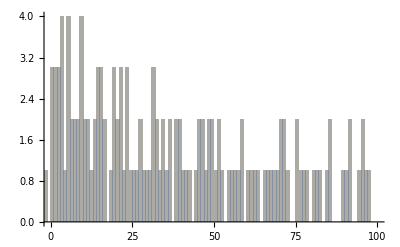

```mathematica
ℏc=197.32858;
Mnucl=(938.2796+939.5731)/2.;
(*lbd=basisdims[[-1]];
parity="-";
J=0.5;
mJ=0.5;
NormHamMat=ReadList["./norm-ham-litME-"<>ToString[J]<>"^"<>parity<>"_1-"<>ToString[lbd],Number];
*)
NormHamMat=ReadList["./MATOUT",Number];
JbasisDim=NormHamMat[[1]];
thr=10^-12;

norm=ArrayReshape[NormHamMat[[2;;JbasisDim^2+1]],{JbasisDim,JbasisDim}];ham=ArrayReshape[NormHamMat[[JbasisDim^2+2;;2 JbasisDim^2+1]],{JbasisDim,JbasisDim}];

decompose[thr,norm,ham];

evhamunnorm=Sort[Eigenvalues[{ham,norm}],Re[#1]>Re[#2]&];
renorm=DiagonalMatrix[1/Sqrt[Diagonal[norm]]];
renormid=DiagonalMatrix[Table[1,{n,JbasisDim}]];
ham=renorm.ham.renorm;norm=renorm.norm.renorm;
evhamnorm=Sort[Eigenvalues[{ham,norm}],Re[#1]>Re[#2]&];

evn=Eigenvalues[norm];

Print["Condition number ℕ_ij = ",Abs[Max[evn]/Min[evn]]];
Print["EV_full(ℍ) = ",evhamnorm[[-4;;]]];
Print["EV_(EV (𝟙) > threshold)(ℍ) = ",Sort[λs,Re[#1]>Re[#2]&][[-4;;]]];

thh=100;(*Max[Abs[λs]];*)

Histogram[{Select[Re[evhamunnorm],Abs[#]<thh&],Re[Select[evhamnorm,Abs[#1]<thh&]]},{1},PlotRange->{{0,thh},Automatic}]
(*Grid[{{"ev(⟨i|j⟩)\n","ev(⟨i|H_nucl|j⟩)","ev(⟨α|H_nucl|β⟩) ev(𝟙) > "ScientificForm[thr]},{Sort[evn,Re[#1]>Re[#2]&]//MatrixForm,Sort[Eigenvalues[{ham,norm}],R~e[#1]>Re[#2]&]//MatrixForm,Sort[λs,Re[#1]>Re[#2]&]//MatrixForm}}]*)
```

```mathematica
HamMat=ReadList["./MATOUTN",Number];
JbasisDim2=HamMat[[1]];

thr2=6^-6;

ham2=ArrayReshape[HamMat[[2;;]],{JbasisDim2,JbasisDim2}];

evhamunnorm2=Sort[Eigenvalues[ham2],Re[#1]>Re[#2]&];
(*renorm=DiagonalMatrix[1/Sqrt[Diagonal[norm]]];
renormid=DiagonalMatrix[Table[1,{n,JbasisDim}]];
ham=renorm.ham.renorm;norm=renorm.norm.renorm;
evhamnorm=Sort[Eigenvalues[{ham,norm}],Re[#1]>Re[#2]&];
*)
(*Print["Condition number ℕ_ij = ",Abs[Max[evn]/Min[evn]]];*)
Print["EV_full(ℍ) = ",evhamunnorm2[[;;]]];
Print["EV_(EV (𝟙) > threshold)(ℍ) = ",Sort[λs,Re[#1]>Re[#2]&][[;;4]]];
```

ReadList::noopen: Cannot open ./MATOUTN.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Part::take: Cannot take positions 2 through -1 in $Failed.

ArrayReshape::listrp: List or SparseArray or StructuredArray expected at position 1 in ArrayReshape[$Failed⟦2;;All⟧,{$Failed⟦1⟧,$Failed⟦1⟧}].

EV_full(ℍ) = Eigenvalues[ArrayReshape[$Failed⟦2;;All⟧,{$Failed⟦1⟧,$Failed⟦1⟧}]]

EV_(EV (𝟙) > threshold)(ℍ) = {105.389,95.3526,79.9913,79.6088}

```mathematica
NormHamMat=ReadList["./MATOUT",Number];
JbasisDim=NormHamMat[[1]];
thr=6^-22;

norm=ArrayReshape[NormHamMat[[2;;JbasisDim^2+1]],{JbasisDim,JbasisDim}];ham=ArrayReshape[NormHamMat[[JbasisDim^2+2;;2 JbasisDim^2+1]],{JbasisDim,JbasisDim}];
evhamunnorm=Sort[Eigenvalues[{ham,norm}],Re[#1]>Re[#2]&];
renorm=DiagonalMatrix[1/Sqrt[Diagonal[norm]]];
renormid=DiagonalMatrix[Table[1,{n,JbasisDim}]];
ham=renorm.ham.renorm;norm=renorm.norm.renorm;

Print[ham//MatrixForm];
Print[norm//MatrixForm];
{ew,ev}=Eigensystem[{ham,norm}];
Print[Re[ew[[-1]]]];
Print[Re[ev[[-1]]]];
```

(498.913 | 413.729 | 0.193091 | 355.82 | 299.008 | 0.119515 | 2.35503 | 1.88231 | 0.000689041 | -330.051 | -201.773 | -54.042 | -309.807 | -184.645 | -45.6767 | -168.877 | -104.943 | -24.9127
413.729 | 390.742 | 0.309105 | 274.391 | 265.453 | 0.184997 | 1.20512 | 1.1733 | 0.000845381 | -234.458 | -142.759 | -37.5975 | -245.722 | -146.166 | -35.405 | -174.766 | -110.714 | -26.2762
0.193091 | 0.309105 | 246.34 | 0.0922916 | 0.172688 | 147.134 | -0.0025142 | -0.00445085 | 0.556666 | -0.0598013 | -0.0335117 | -0.00801349 | -0.0945632 | -0.0524047 | -0.00957229 | -0.284241 | -0.240971 | -0.0764334
355.82 | 274.391 | 0.0922916 | 324.959 | 254.537 | 0.0705052 | 3.7833 | 2.85112 | 0.000591709 | -339.644 | -244.539 | -83.0399 | -294.287 | -205.349 | -63.6976 | -135.882 | -96.8456 | -27.4648
299.008 | 265.453 | 0.172688 | 254.537 | 227.832 | 0.118512 | 2.46796 | 2.08511 | 0.000622703 | -248.014 | -180.732 | -62.4158 | -236.522 | -166.142 | -51.5664 | -142.921 | -102.942 | -28.743
0.119515 | 0.184997 | 147.134 | 0.0705052 | 0.118512 | 96.9262 | -0.0010055 | -0.00202223 | 0.262332 | -0.0547977 | -0.0373194 | -0.0105347 | -0.0729095 | -0.0461404 | -0.00817689 | -0.195478 | -0.173106 | -0.0500328
2.35503 | 1.20512 | -0.0025142 | 3.7833 | 2.46796 | -0.0010055 | 100.755 | 76.6027 | 0.000148527 | -5.05438 | -5.62765 | -4.08388 | -3.8575 | -4.35722 | -3.17458 | -0.899082 | -1.17027 | -1.36943
1.88231 | 1.1733 | -0.00445085 | 2.85112 | 2.08511 | -0.00202223 | 76.6027 | 67.2016 | 0.000246931 | -3.71424 | -4.54014 | -4.44256 | -3.00516 | -3.65207 | -3.45707 | -0.877034 | -1.20496 | -1.68155
0.000689041 | 0.000845381 | 0.556666 | 0.000591709 | 0.000622703 | 0.262332 | 0.000148527 | 0.000246931 | 0.171505 | -0.000878171 | -0.001353 | -0.00513539 | -0.000651362 | -0.000797852 | -0.0024046 | -0.000633378 | -0.000572359 | -0.000229184
-330.051 | -234.458 | -0.0598013 | -339.644 | -248.014 | -0.0547977 | -5.05438 | -3.71424 | -0.000878171 | 466.646 | 385.985 | 160.253 | 340.528 | 278.516 | 109.032 | 100.113 | 88.7065 | 34.8489
-201.773 | -142.759 | -0.0335117 | -244.539 | -180.732 | -0.0373194 | -5.62765 | -4.54014 | -0.001353 | 385.985 | 388.79 | 229.217 | 271.127 | 274.11 | 154.519 | 59.2113 | 73.7786 | 46.3396
-54.042 | -37.5975 | -0.00801349 | -83.0399 | -62.4158 | -0.0105347 | -4.08388 | -4.44256 | -0.00513539 | 160.253 | 229.217 | 327.733 | 107.509 | 157.655 | 219.625 | 7.14522 | 30.4564 | 64.6351
-309.807 | -245.722 | -0.0945632 | -294.287 | -236.522 | -0.0729095 | -3.8575 | -3.00516 | -0.000651362 | 340.528 | 271.127 | 107.509 | 284.299 | 219.856 | 79.9682 | 118.87 | 94.1607 | 31.4283
-184.645 | -146.166 | -0.0524047 | -205.349 | -166.142 | -0.0461404 | -4.35722 | -3.65207 | -0.000797852 | 278.516 | 274.11 | 157.655 | 219.856 | 212.869 | 114.26 | 70.9453 | 74.787 | 39.7317
-45.6767 | -35.405 | -0.00957229 | -63.6976 | -51.5664 | -0.00817689 | -3.17458 | -3.45707 | -0.0024046 | 109.032 | 154.519 | 219.625 | 79.9682 | 114.26 | 156.319 | 10.3402 | 26.6967 | 50.3007
-168.877 | -174.766 | -0.284241 | -135.882 | -142.921 | -0.195478 | -0.899082 | -0.877034 | -0.000633378 | 100.113 | 59.2113 | 7.14522 | 118.87 | 70.9453 | 10.3402 | 137.274 | 95.5855 | 21.024
-104.943 | -110.714 | -0.240971 | -96.8456 | -102.942 | -0.173106 | -1.17027 | -1.20496 | -0.000572359 | 88.7065 | 73.7786 | 30.4564 | 94.1607 | 74.787 | 26.6967 | 95.5855 | 81.5139 | 27.5781
-24.9127 | -26.2762 | -0.0764334 | -27.4648 | -28.743 | -0.0500328 | -1.36943 | -1.68155 | -0.000229184 | 34.8489 | 46.3396 | 64.6351 | 31.4283 | 39.7317 | 50.3007 | 21.024 | 27.5781 | 33.5341)

(1. | 0.942449 | 0.000659538 | 0.88286 | 0.864374 | 0.000586234 | 0.00859047 | 0.00849035 | 7.87647×10^-6 | -0.725616 | -0.515821 | -0.16987 | -0.828289 | -0.589506 | -0.188274 | -0.603711 | -0.467705 | -0.157417
0.942449 | 1. | 0.0011435 | 0.799191 | 0.890077 | 0.00101119 | 0.00586605 | 0.00705613 | 0.0000126745 | -0.613189 | -0.446337 | -0.151876 | -0.77675 | -0.567998 | -0.188345 | -0.717752 | -0.576347 | -0.203936
0.000659538 | 0.0011435 | 1. | 0.000478925 | 0.000955251 | 0.915605 | -0.0000549958 | -0.0000905686 | 0.0110497 | -0.000292198 | -0.000230862 | -0.0000885141 | -0.000546391 | -0.000448299 | -0.000176416 | -0.00190019 | -0.00205056 | -0.00118533
0.88286 | 0.799191 | 0.000478925 | 1. | 0.938137 | 0.00054315 | 0.0182557 | 0.0171337 | 0.0000133441 | -0.881021 | -0.727617 | -0.298807 | -0.969492 | -0.801021 | -0.318722 | -0.655316 | -0.588462 | -0.246296
0.864374 | 0.890077 | 0.000955251 | 0.938137 | 1. | 0.00103028 | 0.0152309 | 0.0162113 | 0.0000222166 | -0.775806 | -0.661806 | -0.286348 | -0.941971 | -0.803611 | -0.336708 | -0.810492 | -0.750931 | -0.330576
0.000586234 | 0.00101119 | 0.915605 | 0.00054315 | 0.00103028 | 1. | -0.0000914625 | -0.000150627 | 0.018554 | -0.00036284 | -0.000347084 | -0.00018343 | -0.000638399 | -0.000624784 | -0.000333781 | -0.00214449 | -0.00257917 | -0.0018678
0.00859047 | 0.00586605 | -0.0000549958 | 0.0182557 | 0.0152309 | -0.0000914625 | 1. | 0.950165 | 0.000526208 | -0.0184912 | -0.0245066 | -0.0274137 | -0.0196534 | -0.0272988 | -0.0339943 | -0.00900785 | -0.0156613 | -0.0336986
0.00849035 | 0.00705613 | -0.0000905686 | 0.0171337 | 0.0162113 | -0.000150627 | 0.950165 | 1. | 0.000873227 | -0.0165564 | -0.0235308 | -0.0325198 | -0.0191138 | -0.0280006 | -0.0413938 | -0.0113385 | -0.020012 | -0.0457571
7.87647×10^-6 | 0.0000126745 | 0.0110497 | 0.0000133441 | 0.0000222166 | 0.018554 | 0.000526208 | 0.000873227 | 1. | -0.000010959 | -0.0000203233 | -0.0000855444 | -0.0000174037 | -0.0000322717 | -0.000131506 | -0.0000469727 | -0.0000945542 | -0.000404538
-0.725616 | -0.613189 | -0.000292198 | -0.881021 | -0.775806 | -0.00036284 | -0.0184912 | -0.0165564 | -0.000010959 | 1. | 0.913959 | 0.434465 | 0.93053 | 0.860873 | 0.401521 | 0.417318 | 0.438185 | 0.224869
-0.515821 | -0.446337 | -0.000230862 | -0.727617 | -0.661806 | -0.000347084 | -0.0245066 | -0.0235308 | -0.0000203233 | 0.913959 | 1. | 0.658904 | 0.839984 | 0.939745 | 0.612905 | 0.319915 | 0.439677 | 0.337069
-0.16987 | -0.151876 | -0.0000885141 | -0.298807 | -0.286348 | -0.00018343 | -0.0274137 | -0.0325198 | -0.0000855444 | 0.434465 | 0.658904 | 1. | 0.396459 | 0.624036 | 0.944694 | 0.0885722 | 0.24643 | 0.531378
-0.828289 | -0.77675 | -0.000546391 | -0.969492 | -0.941971 | -0.000638399 | -0.0196534 | -0.0191138 | -0.0000174037 | 0.93053 | 0.839984 | 0.396459 | 1. | 0.905496 | 0.415541 | 0.629356 | 0.62473 | 0.304978
-0.589506 | -0.567998 | -0.000448299 | -0.801021 | -0.803611 | -0.000624784 | -0.0272988 | -0.0280006 | -0.0000322717 | 0.860873 | 0.939745 | 0.624036 | 0.905496 | 1. | 0.652097 | 0.496887 | 0.628995 | 0.458755
-0.188274 | -0.188345 | -0.000176416 | -0.318722 | -0.336708 | -0.000333781 | -0.0339943 | -0.0413938 | -0.000131506 | 0.401521 | 0.612905 | 0.944694 | 0.415541 | 0.652097 | 1. | 0.151666 | 0.344813 | 0.705339
-0.603711 | -0.717752 | -0.00190019 | -0.655316 | -0.810492 | -0.00214449 | -0.00900785 | -0.0113385 | -0.0000469727 | 0.417318 | 0.319915 | 0.0885722 | 0.629356 | 0.496887 | 0.151666 | 1. | 0.905655 | 0.354974
-0.467705 | -0.576347 | -0.00205056 | -0.588462 | -0.750931 | -0.00257917 | -0.0156613 | -0.020012 | -0.0000945542 | 0.438185 | 0.439677 | 0.24643 | 0.62473 | 0.628995 | 0.344813 | 0.905655 | 1. | 0.59264
-0.157417 | -0.203936 | -0.00118533 | -0.246296 | -0.330576 | -0.0018678 | -0.0336986 | -0.0457571 | -0.000404538 | 0.224869 | 0.337069 | 0.531378 | 0.304978 | 0.458755 | 0.705339 | 0.354974 | 0.59264 | 1.)

0.169677

{0.0000144633,-0.0000171926,-0.0070328,-0.0000206754,0.0000144441,0.00800464,3.88032×10^-6,-6.27365×10^-6,0.999943,0.0000848975,-0.00016361,0.000165051,-0.0000994664,0.000180805,-0.000191662,-0.0000105861,0.0000206785,-0.0000311759}

```mathematica
tt={18959,-30271,
-25900 ,28852, 16076}/10000;

tt/ev[[-1]]
```

Thread::tdlen: Objects of unequal length in {18959/10000,-30271/10000,-259/100,7213/2500,4019/2500} {-61088.4+0. ⅈ,26161.6+0. ⅈ,-35712.+0. ⅈ,3.38195×10^6+0. ⅈ,14640.7+0. ⅈ,«42»,-10956.2+0. ⅈ,-89280.3+0. ⅈ,189165.+0. ⅈ,«253»} cannot be combined.

{18959/10000,-30271/10000,-259/100,7213/2500,4019/2500} {-61088.4+0. ⅈ,26161.6+0. ⅈ,-35712.+0. ⅈ,3.38195×10^6+0. ⅈ,14640.7+0. ⅈ,-6494.89+0. ⅈ,8445.22+0. ⅈ,-251412.+0. ⅈ,-574.914+0. ⅈ,289.086+0. ⅈ,-346.4+0. ⅈ,25806.7+0. ⅈ,438.669+0. ⅈ,-230.108+0. ⅈ,270.678+0. ⅈ,-91214.+0. ⅈ,-85.4888+0. ⅈ,47.2367+0. ⅈ,-49.9007+0. ⅈ,-109.823+0. ⅈ,-51.9971+0. ⅈ,-2.16266+0. ⅈ,2.66786+0. ⅈ,2.88645+0. ⅈ,32.2841+0. ⅈ,2.26077+0. ⅈ,-2.81159+0. ⅈ,-2.96414+0. ⅈ,-1051.81+0. ⅈ,-4621.24+0. ⅈ,-34276.5+0. ⅈ,219076.+0. ⅈ,-1440.1+0. ⅈ,1003.47+0. ⅈ,-1573.93+0. ⅈ,-107001.+0. ⅈ,1131.73+0. ⅈ,-686.973+0. ⅈ,1021.68+0. ⅈ,-622391.+0. ⅈ,-456.243+0. ⅈ,226.181+0. ⅈ,-322.027+0. ⅈ,14195.1+0. ⅈ,513.404+0. ⅈ,-248.338+0. ⅈ,349.349+0. ⅈ,-10956.2+0. ⅈ,-89280.3+0. ⅈ,189165.+0. ⅈ,61433.9+0. ⅈ,-72093.2+0. ⅈ,78513.4+0. ⅈ,-33793.6+0. ⅈ,55876.5+0. ⅈ,-323389.+0. ⅈ,-157969.+0. ⅈ,101090.+0. ⅈ,-264251.+0. ⅈ,-15470.4+0. ⅈ,1.60758×10^6+0. ⅈ,-1.19267×10^6+0. ⅈ,1.40898×10^6+0. ⅈ,23144.5+0. ⅈ,-5054.12+0. ⅈ,4661.85+0. ⅈ,-12932.8+0. ⅈ,3322.51+0. ⅈ,-3396.19+0. ⅈ,11923.3+0. ⅈ,-3235.5+0. ⅈ,7250.95+0. ⅈ,-25388.9+0. ⅈ,3409.53+0. ⅈ,-8995.45+0. ⅈ,-2845.35+0. ⅈ,3199.7+0. ⅈ,1297.74+0. ⅈ,939.709+0. ⅈ,-863.444+0. ⅈ,-1771.58+0. ⅈ,-1398.2+0. ⅈ,1346.31+0. ⅈ,2671.19+0. ⅈ,-87839.3+0. ⅈ,18245.4+0. ⅈ,-12023.1+0. ⅈ,446843.+0. ⅈ,-46216.+0. ⅈ,24783.+0. ⅈ,-124482.+0. ⅈ,58180.5+0. ⅈ,-81903.2+0. ⅈ,2.44349×10^6+0. ⅈ,-1.00692×10^6+0. ⅈ,-3.3176×10^6+0. ⅈ,2050.54+0. ⅈ,519.444+0. ⅈ,3436.64+0. ⅈ,-1664.71+0. ⅈ,-476.818+0. ⅈ,-3120.06+0. ⅈ,275.381+0. ⅈ,543.743+0. ⅈ,2486.8+0. ⅈ,-254.488+0. ⅈ,-569.504+0. ⅈ,-2467.4+0. ⅈ,-2055.76+0. ⅈ,-4688.84+0. ⅈ,-2.21957×10^6+0. ⅈ,270.681+0. ⅈ,715.754+0. ⅈ,9850.+0. ⅈ,-20.6589+0. ⅈ,-71.9685+0. ⅈ,-1312.44+0. ⅈ,6.72902+0. ⅈ,29.0412+0. ⅈ,547.247+0. ⅈ,-8.72094+0. ⅈ,-45.7234+0. ⅈ,-873.663+0. ⅈ,6.36482+0. ⅈ,-38.7276+0. ⅈ,-4303.21+0. ⅈ,-6.8585+0. ⅈ,37.0415+0. ⅈ,4307.49+0. ⅈ,860.926+0. ⅈ,-1694.46+0. ⅈ,26238.2+0. ⅈ,-6306.71+0. ⅈ,7734.52+0. ⅈ,-12537.2+0. ⅈ,14519.3+0. ⅈ,-22210.4+0. ⅈ,9112.81+0. ⅈ,1.6983×10^6+0. ⅈ,2.32123×10^6+0. ⅈ,-13760.1+0. ⅈ,-592268.+0. ⅈ,-802912.+0. ⅈ,30072.2+0. ⅈ,4.58779×10^6+0. ⅈ,-1.77265×10^6+0. ⅈ,1.38696×10^6+0. ⅈ,-2.64254×10^6+0. ⅈ,-297.443+0. ⅈ,145.163+0. ⅈ,-135.155+0. ⅈ,207.284+0. ⅈ,258.423+0. ⅈ,-126.897+0. ⅈ,118.253+0. ⅈ,-180.947+0. ⅈ,-1793.17+0. ⅈ,937.928+0. ⅈ,-880.296+0. ⅈ,1315.18+0. ⅈ,16427.6+0. ⅈ,-12472.+0. ⅈ,12179.+0. ⅈ,-14803.4+0. ⅈ,31870.4+0. ⅈ,5101.08+0. ⅈ,2091.99+0. ⅈ,18631.6+0. ⅈ,-11533.7+0. ⅈ,-3499.62+0. ⅈ,889.994+0. ⅈ,-4620.81+0. ⅈ,14018.1+0. ⅈ,6566.93+0. ⅈ,-1809.48+0. ⅈ,5433.8+0. ⅈ,-190626.+0. ⅈ,147082.+0. ⅈ,-554243.+0. ⅈ,94026.9+0. ⅈ,-1.86812×10^6+0. ⅈ,195914.+0. ⅈ,-140702.+0. ⅈ,482002.+0. ⅈ,-40004.6+0. ⅈ,13987.1+0. ⅈ,-90289.8+0. ⅈ,-37518.2+0. ⅈ,40479.3+0. ⅈ,-12318.2+0. ⅈ,86495.6+0. ⅈ,33691.6+0. ⅈ,-708561.+0. ⅈ,58775.2+0. ⅈ,3.59704×10^6+0. ⅈ,-314151.+0. ⅈ,1.31612×10^6+0. ⅈ,-920429.+0. ⅈ,62722.9+0. ⅈ,613277.+0. ⅈ,-161212.+0. ⅈ,90635.8+0. ⅈ,-70798.4+0. ⅈ,-88624.6+0. ⅈ,174835.+0. ⅈ,-96026.2+0. ⅈ,78252.2+0. ⅈ,95584.1+0. ⅈ,1.27931×10^6+0. ⅈ,-481748.+0. ⅈ,667721.+0. ⅈ,-239588.+0. ⅈ,141786.+0. ⅈ,-230904.+0. ⅈ,-131623.+0. ⅈ,167134.+0. ⅈ,-2.39121×10^6+0. ⅈ,268036.+0. ⅈ,887857.+0. ⅈ,-239799.+0. ⅈ,2.15995×10^6+0. ⅈ,-382531.+0. ⅈ,450863.+0. ⅈ,539097.+0. ⅈ,-515016.+0. ⅈ,3.41881×10^6+0. ⅈ,-374719.+0. ⅈ,299474.+0. ⅈ,-3.21165×10^6+0. ⅈ,128340.+0. ⅈ,-46167.2+0. ⅈ,15224.9+0. ⅈ,-168068.+0. ⅈ,53266.4+0. ⅈ,-13312.3+0. ⅈ,-1.42935×10^6+0. ⅈ,287370.+0. ⅈ,62983.+0. ⅈ,-939858.+0. ⅈ,2.71101×10^6+0. ⅈ,-208697.+0. ⅈ,87194.8+0. ⅈ,309172.+0. ⅈ,-182634.+0. ⅈ,1.09717×10^6+0. ⅈ,-760185.+0. ⅈ,-452473.+0. ⅈ,293146.+0. ⅈ,572762.+0. ⅈ,384804.+0. ⅈ,-262427.+0. ⅈ,-287856.+0. ⅈ,-852150.+0. ⅈ,484165.+0. ⅈ,244680.+0. ⅈ,2.60825×10^6+0. ⅈ,-2.06769×10^6+0. ⅈ,-268617.+0. ⅈ,-5.59609×10^6+0. ⅈ,3.3132×10^6+0. ⅈ,-738206.+0. ⅈ,1.9711×10^6+0. ⅈ,-1.20975×10^6+0. ⅈ,-3.34022×10^7+0. ⅈ,6.84958×10^7+0. ⅈ,-285062.+0. ⅈ,146495.+0. ⅈ,-149300.+0. ⅈ,-3.3483×10^6+0. ⅈ,80262.4+0. ⅈ,-80226.6+0. ⅈ,78736.+0. ⅈ,383055.+0. ⅈ,-30735.9+0. ⅈ,24473.+0. ⅈ,-46740.1+0. ⅈ,-207914.+0. ⅈ,36231.+0. ⅈ,-25385.4+0. ⅈ,54809.+0. ⅈ,277660.+0. ⅈ,-105774.+0. ⅈ,71551.5+0. ⅈ,-151579.+0. ⅈ,-1.58068×10^6+0. ⅈ,-8.01606×10^6+0. ⅈ,2.0471×10^7+0. ⅈ,-528453.+0. ⅈ,-4.9177×10^7+0. ⅈ,-177438.+0. ⅈ,4.00295×10^6+0. ⅈ,48192.8+0. ⅈ,-23187.9+0. ⅈ,-973130.+0. ⅈ,-43718.6+0. ⅈ,20671.8+0. ⅈ,993177.+0. ⅈ,2902.45+0. ⅈ,-1594.19+0. ⅈ,-1389.66+0. ⅈ,-2922.37+0. ⅈ,1607.04+0. ⅈ,1382.41+0. ⅈ}